```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

c::shdw: Symbol c appears in multiple contexts {BFSS2`,Global`}; definitions in context BFSS2` may shadow or be shadowed by other definitions.

$N::shdw: Symbol $N appears in multiple contexts {BFSS2`,Global`}; definitions in context BFSS2` may shadow or be shadowed by other definitions.

$K::shdw: Symbol $K appears in multiple contexts {BFSS2`,Global`}; definitions in context BFSS2` may shadow or be shadowed by other definitions.

```mathematica
changeNK[9, 9]
```

```mathematica
data = Import["../../../runs/Trials/N9K9/15650383.dat"];
```

```mathematica
data//Length
```

100000

```mathematica
1/1024^3 MemoryInUse[]//N
```

5.21106

```mathematica
ClearAll[data]
```

```mathematica
$N=9;$K=9;
```

```mathematica
l = Flatten@data[[All, 2;;$K(($N)^2-1)+1]];
```

```mathematica
hist = Histogram[l, 400, PDF];
```

```mathematica
α = 2/(StandardDeviation[l]^2 $N);
```

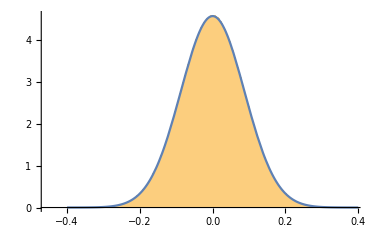

```mathematica
Show[
hist,
Plot[√((α $N)/(4π))Exp[-(α $N)/4 x^2], {x, -0.4, 0.4}]
]
```

```mathematica
c = Covariance[data[[All, 2;;$K(($N)^2-1)+1]]];
```

```mathematica
Dimensions[c]
```

{720,720}

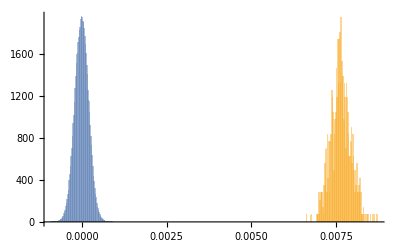

```mathematica
Histogram[{Table[c[[i, i]], {i, 1, $K(($N)^2-1)}], Flatten@Table[c[[i, j]], {i, 1, $K(($N)^2-1)}, {j,i+1,$K($N^2-1)}]}, 300, PDF, PlotRange->All]
```

```mathematica
x = Partition[#, ($N)^2-1]&/@data[[All, 2;;$K(($N)^2-1)+1]];
p = Partition[#, ($N)^2-1]&/@data[[All, $K(($N)^2-1)+2;;]];
```

```mathematica
G = Monitor[Table[
{data[[k, 1]], Table[Sum[
$fSU[[cc, aa, bb]]x[[k, i, aa]]p[[k, i, bb]]
, {i, 1, $K}, {aa, 1, ($N)^2-1}, {bb, 1, ($N)^2-1}], {cc, 1, ($N)^2-1}]}
, {k, 1, 10}], ProgressIndicator[(k-1)/(Length[x]-1)]];
```

$Aborted

```mathematica
G = Table[Sum[
$fSU[[1, aa, bb]]x[[k, i, aa]]p[[k, i, bb]]
, {i, 1, $K}, {aa, 1, ($N)^2-1}, {bb, 1, ($N)^2-1}], {k, 99990, 100000}];
```

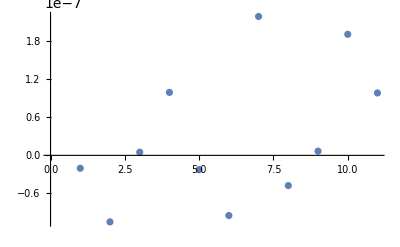

```mathematica
ListPlot[G]
```

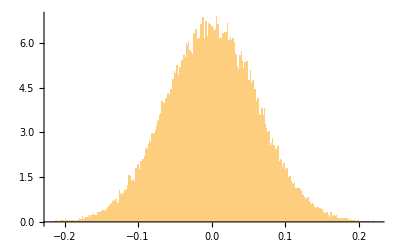

```mathematica
Histogram[data[[All, $K(($N)^2-1)+2]], 400, PDF]
```